```mathematica
u090494e　荒井直幸　2014年10月28日
```

```mathematica
課題１
```

```mathematica
L1=L2の時に縮退が起こる。
```

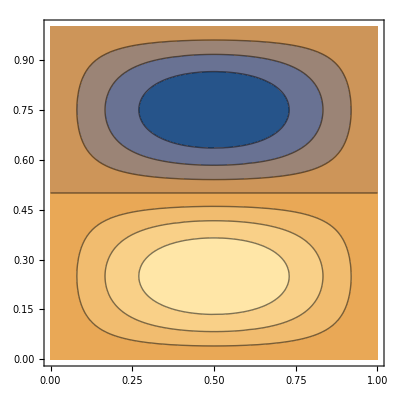

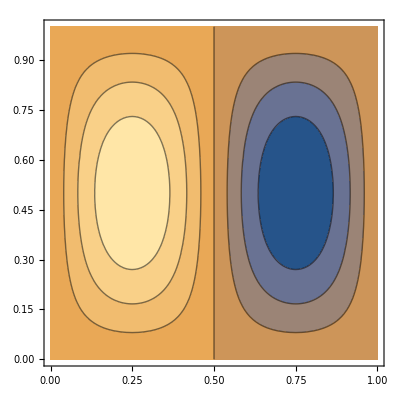

```mathematica
hako[1,2,1,1]
hako[2,1,1,1]
```

```mathematica
課題２
```

```mathematica
f1=Plot[x^2,{x,-1,10},PlotRange->{0,1},PlotStyle->{RGBColor[0,1,0]}];
f2=Plot[(1-Exp[-x])^2,{x,-1,10},PlotRange->{0,1},PlotStyle->{RGBColor[1,0,0]}];
```

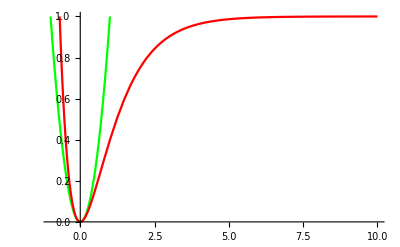

```mathematica
Show[f1,f2]
```

```mathematica
課題３
```

```mathematica
g1=SphericalPlot3D[Abs[SphericalHarmonicY[2,-2,theta,phi]]^2,{theta,0,Pi},{phi,0,2Pi}]
g2=SphericalPlot3D[Abs[SphericalHarmonicY[2,-1,theta,phi]]^2,{theta,0,Pi},{phi,0,2Pi}]
g3=SphericalPlot3D[Abs[SphericalHarmonicY[2,0,theta,phi]]^2,{theta,0,Pi},{phi,0,2Pi}]
g4=SphericalPlot3D[Abs[SphericalHarmonicY[2,1,theta,phi]]^2,{theta,0,Pi},{phi,0,2Pi}]
g5=SphericalPlot3D[Abs[SphericalHarmonicY[2,2,theta,phi]]^2,{theta,0,Pi},{phi,0,2Pi}]
Show[g1,g2,g3,g4,g5,PlotRange->{{-0.2,0.2},{-0.2,0.2},{-0.4,0.4}}]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«3 more identical outputs»

```mathematica
課題４
```

```mathematica
h1=SphericalPlot3D[Abs[-SphericalHarmonicY[2,1,theta,phi]+SphericalHarmonicY[2,-1,theta,phi]]^2/2,{theta,0,Pi},{phi,0,2Pi},PlotRange->All]
h2=SphericalPlot3D[Abs[SphericalHarmonicY[2,1,theta,phi]+SphericalHarmonicY[2,-1,theta,phi]]^2/2,{theta,0,Pi},{phi,0,2Pi},PlotRange->All]
h3=SphericalPlot3D[Abs[-SphericalHarmonicY[2,2,theta,phi]+SphericalHarmonicY[2,-2,theta,phi]]^2/2,{theta,0,Pi},{phi,0,2Pi},PlotRange->All]
h4=SphericalPlot3D[Abs[SphericalHarmonicY[2,2,theta,phi]+SphericalHarmonicY[2,-2,theta,phi]]^2/2,{theta,0,Pi},{phi,0,2Pi},PlotRange->All]
h5=SphericalPlot3D[Abs[SphericalHarmonicY[2,0,theta,phi]+SphericalHarmonicY[2,0,theta,phi]]^2/2,{theta,0,Pi},{phi,0,2Pi},PlotRange->All]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«2 more identical outputs»